```mathematica
f1[u_]:={Sin[u],Cos[u]}
f2[u_]:={(5-0.2 u) Sin[u],Cos[u]}
```

```mathematica
Manipulate[ParametricPlot3D[Append[v*f1[u]+(1-v) f2[u],v],{u,0,umax},{v,0,vmax},BoxRatios->{1,1,1}, AxesLabel->Automatic], {umax, 0.1, 2*Pi}, {vmax, 0.1, 1}]
```

```mathematica
f0102[u_]:= {(u*20*(3)^(1/2)/(300*(19)^(1/2))), (1/80)*(u*20*(3)^(1/2)/(300*(19)^(1/2)))^2}
f0201[u_]:= {u*5*(57)^(1/2)/(300*(19)^(1/2)), (1/95)*(u*5*(57)^(1/2)/(300*(19)^(1/2)))^2}
```

```mathematica
ParametricPlot3D[Append[v*f0102[u]+(1-v) f0201[u],v],{u,-300*(19)^(1/2),300*(19)^(1/2)},{v,0,10},BoxRatios->{1,1,1}, AxesLabel->Automatic]
```

-Graphics3D-

{(u (1-v))/(20 √3)+(u v)/(5 √57),(u^2 (1-v))/114000+(u^2 v)/114000,v}

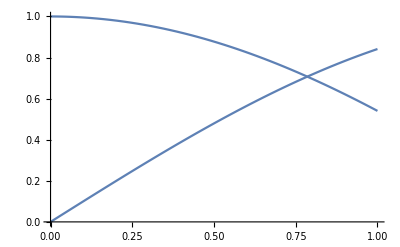

```mathematica
Clear[sweptParabola]
sweptParabola[f1_, f2_]:= Append[v*f1[u]+(1-v) f2[u],v]
surf0102 = sweptParabola[f0102, f0201]
reg0102 = ImplicitRegion[{{x,-40,40},{y,0,15},{z,0,10}}]
```